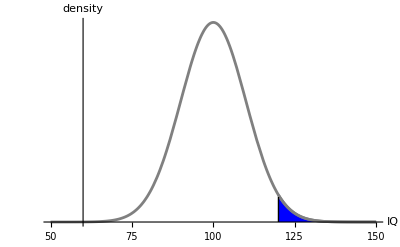

```mathematica
dist=PDF[NormalDistribution[100,10],#]&;
p1=Plot[dist@x,{x,120,150},Filling->Axis,FillingStyle->Blue,PlotRange->{{50,150},All},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{IQ,"density"},Ticks->{True,None}];
p2=Plot[dist@x,{x,50,150},Filling->None,PlotRange->{{50,150},All},BaseStyle->{FontSize->16},PlotStyle->{Gray,Thickness[0.005]},AxesLabel->{IQ,"density"}];
Show[p1,p2,Epilog->{Black,Line[{{120,0},{120,0.005}}],Line[{{0.75,0},{0.75,1}}]}]
```

```mathematica
N[Integrate[PDF[NormalDistribution[100,10],x],{x,120,∞}]]
```

0.0227501